{{X[t]→InterpolatingFunction[…][t],B[t]→InterpolatingFunction[…][t],S[t]→InterpolatingFunction[…][t],CO2[t]→InterpolatingFunction[…][t],CH4[t]→InterpolatingFunction[…][t]}}

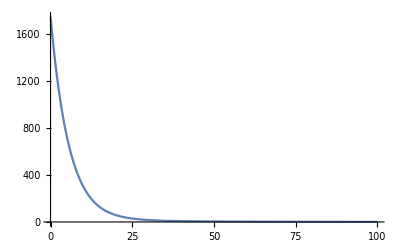

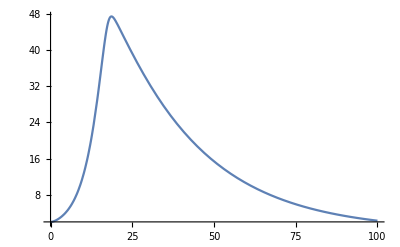

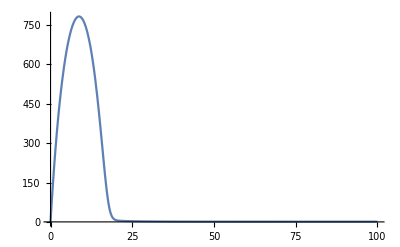

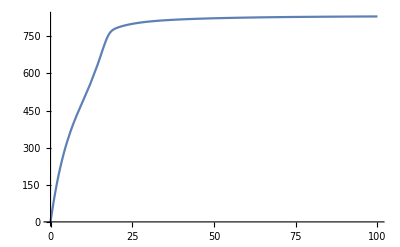

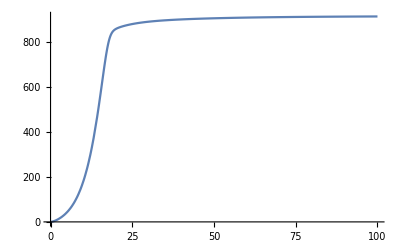

{{0,{0.}},{10,{178.917}},{20,{857.315}},{30,{889.396}},{40,{899.503}},{50,{904.538}},{60,{907.639}},{70,{909.692}},{80,{911.079}},{90,{912.021}},{100,{912.663}}}

0 | 0.
10 | 178.917
20 | 857.315
30 | 889.396
40 | 899.503
50 | 904.538
60 | 907.639
70 | 909.692
80 | 911.079
90 | 912.021
100 | 912.663

RK4 (10) (CH4)[t] value of the system of monod law for B=2.xls

```mathematica
Subscript[K, h]=0.176;
Subscript[μ, m]=0.3;
Subscript[f, 1]=0.7;
Subscript[f, 2]=0.76;
Subscript[K, s]=160;
Subscript[K, d]=0.04;
Y=0.05;
Subscript[K, i]=10;
α=0.9;
sol1=NDSolve[{X'[t]==-Subscript[K, h]*X[t]+α*Subscript[K, d]*B[t],
B'[t]==(((Subscript[μ, m]*S[t])/(Subscript[K, s]+S[t]))-Subscript[K, d])*B[t],
S'[t]==(Subscript[f, 1]*Subscript[K, h]*X[t])-(1/Y)*((Subscript[μ, m]*S[t])/(Subscript[K, s]+S[t]))*B[t],
(CO2)'[t]==(1-Subscript[f, 1])*Subscript[K, h]*X[t]+(1-Subscript[f, 2])*((1-Y)/Y)*((Subscript[μ, m]*S[t])/(Subscript[K, s]+S[t]))*B[t],
(CH4)'[t]==Subscript[f, 2]*((1-Y)/Y)*((Subscript[μ, m]*S[t])/(Subscript[K, s]+S[t]))*B[t],
X[0]==1751,B[0]==2,S[0]==0,(CO2)[0]==0,(CH4)[0]==0},{X[t],B[t],S[t],(CO2)[t],(CH4)[t]},{t,0,100}]
(*Plot[Evaluate[{X[t],B[t],S[t],(CO2)[t],(CH4)[t]}/.sol1],{t,0,100},PlotRange->All]*)
Plot[Evaluate[{X[t]}/.sol1],{t,0,100},PlotRange->All]
Plot[Evaluate[{B[t]}/.sol1],{t,0,100},PlotRange->All]
Plot[Evaluate[{S[t]}/.sol1],{t,0,100},PlotRange->All]
Plot[Evaluate[{(CO2)[t]}/.sol1],{t,0,100},PlotRange->All]
Plot[Evaluate[{(CH4)[t]}/.sol1],{t,0,100},PlotRange->All]
(*tt=Table[{t,{X[t],B[t],S[t],(CO2)[t],(CH4)[t]}/.sol1},{t,0,100,10}]*)
tt=Table[{t,(CH4)[t]/.sol1},{t,0,100,10}]
tt//TableForm
Export["RK4 (10) (CH4)[t] value of the system of monod law for B=2.xls",tt,"XLS"]
```

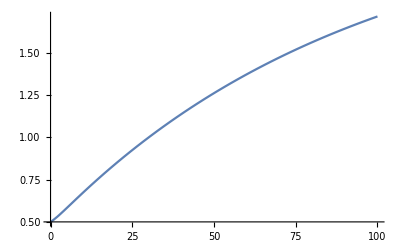

-Graphics-